```mathematica
h[z_]:=1/2(Tanh[z/L]+1)
```

```mathematica
Integrate[((D[h[x],x])/.{x->z})^3,z]
```

(8/15 L Tanh[z/L]+4/15 L Sech[z/L]^2 Tanh[z/L]+1/5 L Sech[z/L]^4 Tanh[z/L])/(8 L^3)

```mathematica
V[ϕ_]:=λ/4 ϕ^2(ϕ-ϕ0)^2
```

```mathematica
Integrate[V[ϕ],{ϕ,0,ϕ0}]
```

(λ ϕ0^5)/120

```mathematica
64/120
```

8/15

# Electroweak baryogenesis at high wall velocities (arXiv:2001.00568)

## Master Code (ms=80 GeV) Gamma denom

```mathematica
(*ClearAll["Global`*"];*)
SetDirectory[NotebookDirectory[]];
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;(*******************************************************************************************************************)
(**********************************************************************************************)
(*gtab=Drop[Import["effectivedof.txt","Table"],3];
gstar[T_]:=Interpolation[gtab[[All,{1,3}]]][T];*)
gtab=Import["standardmodel2018.txt","Table",HeaderLines->8][[;;;;20]];
gstar[T_]:=Interpolation[gtab[[All,{1,2}]]][T];
gsstar[T_]:=Interpolation[gtab[[All,{1,4}]]][T];
(*****************************************************************************************************)
(*****************************************************************************************************)
params3=Import["Wall_Solutions_3/ms_80_total.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
alphalist=params3[All,"alpha"];
betalist=params3[All,"d/dT(S_3/T)"];MasterFunction[Tn_,vw_,h0_,Lh_,s0_,Ls_,ds_,ΛCP_,Infty_,points_]:=MasterFunction[Tn,vw,h0,Lh,s0,Ls,ds,ΛCP,Infty,points]=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
s[z_]:=s0/2(1-Tanh[z/Ls-ds]);(**equation (50)**)
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=gstar[Tn](*106.75*);
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)],{z,-inf,inf},Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"},PlotRange->All];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""},PlotRange->All];
(*Return[Abs[ηB/ηobs]];*)
Return[{Plot1,Plot2,Abs[ηB/ηobs]}];
];(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)MasterOutputOld[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];
MasterPars[i_]:=Print[ "Pars α=",alphalist[[i]],(*" β/H=",betalist[[i]],*)" T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_0=",s0list[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]];
MasterOutput[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];
MasterOutputVelOld[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];
MasterOutputVel[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];
BAUscale[i_]:=Module[{BAU,res},
BAU[Λ_?NumericQ]:=BAU[Λ?NumericQ]=MasterOutputVel[i,Λ,400][[3]];
If[BAU[100]<1,Return[99]];
Quiet[
res=Λ/.FindRoot[BAU[Λ]-1,{Λ,100,1000},AccuracyGoal->2,PrecisionGoal->2(*,EvaluationMonitor:>Print["Λ=",Λ," BAU=",BAU[Λ]]*)];
];
MasterPars[i];
Print["Λ=",res];
Return[res]
];
(*vwdat=Table[vwlist[[i]],{i,1,Length[vwlist]}];*)
```

Pars α=0.0104469 T_n=97.1525 v_w=0.324655 T_p=97.7291 v_p=0.311772 h_0=218.442 L_h=0.0840308 s_0=128.611 L_s=0.0745624 ds=0.902307

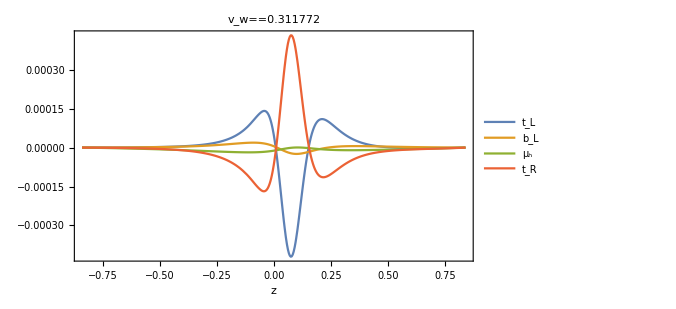
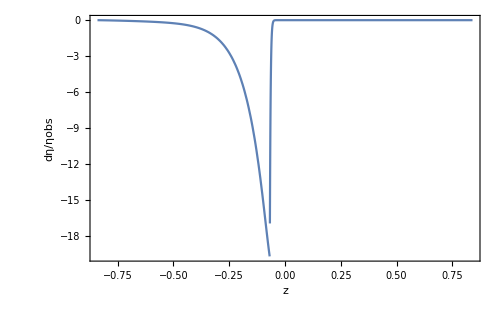
{80.2779,{-Graphics-,-Graphics-,1.77399}}

```mathematica
params3=Import["Wall_Solutions_3/ms_70_root_2.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
alphalist=params3[All,"alpha"];
betalist=params3[All,"d/dT(S_3/T)"];
k0=1;
MasterPars[k0]
Timing[MasterOutputVel[k0,500,400]]
```

```mathematica
k0=2;
MasterPars[k0]
BAUscale[k0]
```

Pars α=0.00964702 T_n=102.071 v_w=0.430407 T_p=103.344 v_p=0.409472 h_0=212.528 L_h=0.0664209 s_0=124.379 L_s=0.0567792 ds=0.867478

Pars α=0.00964702 T_n=102.071 v_w=0.430407 T_p=103.344 v_p=0.409472 h_0=212.528 L_h=0.0664209 s_0=124.379 L_s=0.0567792 ds=0.867478

Λ=681.22

681.22

```mathematica
params3=Import["Wall_Solutions_3/ms_70_root_2.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
alphalist=params3[All,"alpha"];
betalist=params3[All,"d/dT(S_3/T)"];
BAULambda=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["BAU_DATA_1/BAULambdams80.csv",BAULambda]
```

Pars Î±=0.0104469 T =97.1525 v =0.324655 T =97.7291 v =0.311772 h =218.442 L =
                   n          w           p          p           0          h
 
>   0.0840308 s =128.611 L =0.0745624 ds=0.902307
               0          s

Î.9b=906.232

Pars Î±=0.0133936 T =91.1659 v =0.426495 T =92.6423 v =0.398895 h =222.814 L =
                   n          w           p          p           0          h
 
>   0.0678875 s =130.927 L =0.0592574 ds=0.88207
               0          s

Î.9b=779.36

Pars Î±=0.0149634 T =88.5654 v =0.460358 T =90.6406 v =0.423149 h =224.382 L =
                   n          w           p          p           0          h
 
>   0.0631867 s =131.836 L =0.0549422 ds=0.874341
               0          s

Î.9b=743.983

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.012286 T =93.2241 v =0.395263 T =94.3205 v =0.373781 h =221.439 L =
                  n          w           p          p           0          h
 
>   0.0724322 s =130.167 L =0.0634935 ds=0.888652
               0          s

Î.9b=822.35

Pars Î±=0.0108051 T =96.3301 v =0.340522 T =96.9959 v =0.326132 h =219.112 L =
                   n          w           p          p           0          h
 
>   0.0811966 s =128.948 L =0.0718278 ds=0.899336
               0          s

Î.9b=891.941

Pars Î±=0.0136512 T =90.7154 v =0.432802 T =92.2857 v =0.403692 h =223.099 L =
                   n          w           p          p           0          h
 
>   0.0669984 s =131.089 L =0.058436 ds=0.880686
               0          s

Î.9b=771.181

Pars Î±=0.0152965 T =88.0548 v =0.466321 T =90.2631 v =0.426967 h =224.67 L =
                   n          w           p          p           0         h
 
>   0.0623753 s =132.008 L =0.0542044 ds=0.872895
               0          s

Î.9b=740.53

Pars Î±=0.0125285 T =92.7547 v =0.402559 T =93.9294 v =0.379814 h =221.765 L =
                   n          w           p          p           0          h
 
>   0.07131 s =130.344 L =0.0624426 ds=0.887106
             0          s

Î.9b=813.046

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,2581,14].

Kernels::rdead: Subkernel connected through KernelObject[3,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {142} assigned to KernelObject[3,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[3,local,<defunct>] resurrected as KernelObject[5,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,2579,12].

Kernels::rdead: Subkernel connected through KernelObject[1,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {144} assigned to KernelObject[1,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[1,local,<defunct>] resurrected as KernelObject[6,local].

Pars Î±=0.0111332 T =95.6023 v =0.355894 T =96.3643 v =0.339907 h =219.675 L =
                   n          w           p          p           0          h
 
>   0.0790687 s =129.241 L =0.0697691 ds=0.896874
               0          s

Î.9b=865.419

Pars Î±=0.0141445 T =89.88 v =0.444007 T =91.6358 v =0.411925 h =223.612 L =
                   n        w           p          p           0          h
 
>   0.0654363 s =131.384 L =0.0569986 ds=0.87817
               0          s

Î.9b=758.281

Pars Î±=0.0149634 T =88.5654 v =0.460358 T =90.6406 v =0.423149 h =224.382 L =
                   n          w           p          p           0          h
 
>   0.0631867 s =131.836 L =0.0549422 ds=0.874341
               0          s

Î.9b=743.983

Pars Î±=0.012286 T =93.2241 v =0.395263 T =94.3205 v =0.373781 h =221.439 L =
                  n          w           p          p           0          h
 
>   0.0724322 s =130.167 L =0.0634935 ds=0.888652
               0          s

Î.9b=822.35

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0113115 T =95.2174 v =0.361147 T =96.0194 v =0.344483 h =219.981 L =
                   n          w           p          p           0          h
 
>   0.077741 s =129.395 L =0.0685179 ds=0.895409
              0          s

Î.9b=867.917

Pars Î±=0.0144015 T =89.458 v =0.449422 T =91.3126 v =0.415755 h =223.864 L =
                   n         w           p          p           0          h
 
>   0.0646875 s =131.531 L =0.0563124 ds=0.876923
               0          s

Î.9b=752.627

Pars Î±=0.0152965 T =88.0548 v =0.466321 T =90.2631 v =0.426967 h =224.67 L =
                   n          w           p          p           0         h
 
>   0.0623753 s =132.008 L =0.0542044 ds=0.872895
               0          s

Î.9b=740.53

Pars Î±=0.0125285 T =92.7547 v =0.402559 T =93.9294 v =0.379814 h =221.765 L =
                   n          w           p          p           0          h
 
>   0.07131 s =130.344 L =0.0624426 ds=0.887106
             0          s

Î.9b=813.046

Pars Î±=0.011715 T =94.3699 v =0.376145 T =95.2889 v =0.357552 h =220.616 L =
                  n          w           p          p           0          h
 
>   0.0753609 s =129.727 L =0.0662555 ds=0.892492
               0          s

Î.9b=848.537

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0146416 T =89.0716 v =0.454275 T =91.0195 v =0.419098 h =224.091 L =
                   n          w           p          p           0          h
 
>   0.0640245 s =131.664 L =0.0557062 ds=0.875795
               0          s

Î.9b=747.163

Pars Î±=0.0155603 T =87.6594 v =0.470781 T =89.9742 v =0.429711 h =224.889 L =
                   n          w           p          p           0          h
 
>   0.0617673 s =132.14 L =0.0536527 ds=0.87179
               0         s

Î.9b=741.008

Pars Î±=0.012761 T =92.3155 v =0.409488 T =93.569 v =0.385467 h =222.062 L =
                  n          w           p         p           0          h
 
>   0.0703184 s =130.508 L =0.0615159 ds=0.885692
               0          s

Î.9b=802.715

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0165153 T =86.2923 v =0.485252 T =88.9981 v =0.43788 h =225.618 L =
                   n          w           p          p          0          h
 
>   0.0598092 s =132.585 L =0.0518838 ds=0.868089
               0          s

Î.9b=733.501

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars Î±=0.0182729 T =84.0076 v =0.506806 T =87.4406 v =0.447566 h =226.752 L =
                   n          w           p          p           0          h
 
>   0.0569517 s =133.298 L =0.0493216 ds=0.862243
               0          s

Î.9b=748.626

Pars Î±=0.0158872 T =87.1805 v =0.476004 T =89.6282 v =0.432795 h =225.149 L =
                   n          w           p          p           0          h
 
>   0.0610586 s =132.297 L =0.0530112 ds=0.870477
               0          s

Î.9b=739.865

Pars Î±=0.0129802 T =91.9099 v =0.415631 T =93.2392 v =0.390393 h =222.332 L =
                   n          w           p          p           0          h
 
>   0.0694327 s =130.657 L =0.0606908 ds=0.884401
               0          s

Î.9b=794.137

Pars Î±=0.0168443 T =85.843 v =0.489756 T =88.6845 v =0.440171 h =225.849 L =
                   n         w           p          p           0          h
 
>   0.0592081 s =132.728 L =0.0513429 ds=0.866905
               0          s

Î.9b=735.324

Pars Î±=0.0187324 T =83.4536 v =0.51161 T =87.0759 v =0.44925 h =227.013 L =
                   n          w          p          p          0          h
 
>   0.0563266 s =133.465 L =0.0487639 ds=0.860889
               0          s

Î.9b=752.678

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,2580,13].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {146} assigned to KernelObject[2,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[2,local,<defunct>] resurrected as KernelObject[7,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

Pars Î±=0.0162249 T =86.6978 v =0.481114 T =89.2839 v =0.435668 h =225.406 L =
                   n          w           p          p           0          h
 
>   0.0603691 s =132.454 L =0.0523884 ds=0.86917
               0          s

Î.9b=733.825

Pars Î±=0.0131844 T =91.5391 v =0.421107 T =92.9403 v =0.394714 h =222.574 L =
                   n          w           p          p           0          h
 
>   0.0686498 s =130.792 L =0.0599636 ds=0.883233
               0          s

Î.9b=786.794

Pars Î±=0.0171842 T =85.3897 v =0.494134 T =88.3721 v =0.442267 h =226.078 L =
                   n          w           p          p           0          h
 
>   0.0586229 s =132.871 L =0.0508174 ds=0.865728
               0          s

Î.9b=739.272

Pars Î±=0.0182729 T =84.0076 v =0.506806 T =87.4406 v =0.447566 h =226.752 L =
                   n          w           p          p           0          h
 
>   0.0569517 s =133.298 L =0.0493216 ds=0.862243
               0          s

Î.9b=748.626

Pars Î±=0.0203551 T =81.6222 v =0.526831 T =85.904 v =0.453347 h =227.838 L =
                   n          w           p         p           0          h
 
>   0.0544252 s =134.001 L =0.0470734 ds=0.856569
               0          s

Î.9b=780.321

Pars Î±=0.0228561 T =79.1236 v =0.54551 T =84.3841 v =0.455495 h =228.881 L =
                   n          w          p          p           0          h
 
>   0.052179 s =134.696 L =0.0450869 ds=0.851058
              0          s

Î.9b=837.313

Pars Î±=0.0175027 T =84.9746 v =0.498084 T =88.0888 v =0.44405 h =226.285 L =
                   n          w           p          p          0          h
 
>   0.0581031 s =133.001 L =0.0503513 ds=0.864665
               0          s

Î.9b=741.242

Pars Î±=0.0187324 T =83.4536 v =0.51161 T =87.0759 v =0.44925 h =227.013 L =
                   n          w          p          p          0          h
 
>   0.0563266 s =133.465 L =0.0487639 ds=0.860889
               0          s

Î.9b=752.678

Pars Î±=0.0178311 T =84.5562 v =0.502029 T =87.8059 v =0.445726 h =226.489 L =
                   n          w           p          p           0          h
 
>   0.0575951 s =133.13 L =0.0498964 ds=0.863607
               0         s

Î.9b=743.842

Pars Î±=0.0208184 T =81.132 v =0.530587 T =85.5991 v =0.454026 h =228.05 L =
                   n         w           p          p           0         h
 
>   0.053955 s =134.141 L =0.0466568 ds=0.855455
              0          s

Î.9b=790.076

Pars Î±=0.0233656 T =78.6558 v =0.548876 T =84.1088 v =0.455552 h =229.066 L =
                   n          w           p          p           0          h
 
>   0.0517972 s =134.821 L =0.0447503 ds=0.850072
               0          s

Î.9b=849.916

Pars Î±=0.019137 T =82.9796 v =0.515745 T =86.7676 v =0.450569 h =227.232 L =
                  n          w           p          p           0          h
 
>   0.0558117 s =133.606 L =0.0483053 ds=0.859747
               0          s

Î.9b=758.431

Pars Î±=0.0259069 T =76.497 v =0.564027 T =82.873 v =0.454615 h =229.887 L =
                   n         w           p         p           0          h
 
>   0.0501706 s =135.382 L =0.0433189 ds=0.845695
               0          s

Î.9b=913.325

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0212546 T =80.6824 v =0.534008 T =85.3223 v =0.454539 h =228.241 L =
                   n          w           p          p           0          h
 
>   0.053537 s =134.267 L =0.0462867 ds=0.854447
              0          s

Î.9b=799.604

Pars Î±=0.0240023 T =78.0886 v =0.552919 T =83.7789 v =0.455493 h =229.287 L =
                   n          w           p          p           0          h
 
>   0.0513492 s =134.971 L =0.0443556 ds=0.848895
               0          s

Î.9b=865.868

Pars Î±=0.0265353 T =76.0038 v =0.567449 T =82.5989 v =0.454153 h =230.066 L =
                   n          w           p          p           0          h
 
>   0.0498282 s =135.506 L =0.0430182 ds=0.844735
               0          s

Î.9b=921.517

Pars Î±=0.0195166 T =82.5457 v =0.519354 T =86.4884 v =0.451589 h =227.429 L =
                   n          w           p          p           0          h
 
>   0.0553542 s =133.733 L =0.0478983 ds=0.858716
               0          s

Î.9b=764.961

Pars Î±=0.0245546 T =77.6116 v =0.556264 T =83.5042 v =0.455332 h =229.47 L =
                   n          w           p          p           0         h
 
>   0.0509839 s =135.096 L =0.0440341 ds=0.84792
               0          s

Î.9b=881.043

Pars Î±=0.021752 T =80.1832 v =0.537742 T =85.0184 v =0.454979 h =228.449 L =
                  n          w           p          p           0          h
 
>   0.0530871 s =134.406 L =0.0458888 ds=0.853345
               0          s

Î.9b=810.899

Pars Î±=0.0273227 T =75.4061 v =0.571534 T =82.27 v =0.453476 h =230.28 L =
                   n          w           p        p           0         h
 
>   0.0494258 s =135.655 L =0.042665 ds=0.84359
               0          s

Î.9b=933.197

Pars Î±=0.0251873 T =77.0812 v =0.559982 T =83.2022 v =0.455051 h =229.67 L =
                   n          w           p          p           0         h
 
>   0.0505904 s =135.233 L =0.0436879 ds=0.846853
               0          s

Î.9b=897.193

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0199087 T =82.1079 v =0.522963 T =86.2097 v =0.452503 h =227.625 L =
                   n          w           p          p           0          h
 
>   0.0549066 s =133.861 L =0.0475006 ds=0.857691
               0          s

Î.9b=771.968

Pars Î±=0.0280092 T =74.9027 v =0.574975 T =81.996 v =0.452815 h =230.457 L =
                   n          w           p         p           0          h
 
>   0.0490976 s =135.779 L =0.0423771 ds=0.842641
               0          s

Î.9b=944.056

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0223168 T =79.6331 v =0.541807 T =84.6872 v =0.455317 h =228.675 L =
                   n          w           p          p           0          h
 
>   0.052608 s =134.557 L =0.0454655 ds=0.852148
              0          s

Î.9b=824.251

Pars Î±=0.029704 T =73.7234 v =0.583112 T =81.3651 v =0.451067 h =230.861 L =
                  n          w           p          p           0          h
 
>   0.0483653 s =136.062 L =0.041735 ds=0.840474
               0          s

Î.9b=971.854

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0332871 T =71.4879 v =0.599147 T =80.2021 v =0.447737 h =231.589 L =
                   n          w           p          p           0          h
 
>   0.0471033 s =136.576 L =0.0406295 ds=0.836548
               0          s

Î.9b=1027.24

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0304925 T =73.2025 v =0.586738 T =81.0894 v =0.450289 h =231.035 L =
                   n          w           p          p           0          h
 
>   0.0480562 s =136.185 L =0.0414643 ds=0.839533
               0          s

Î.9b=984.543

Pars Î±=0.0903435 T =54.5643 v =0.743895 T =72.6702 v =0.423872 h =235.794 L =
                   n          w           p          p           0          h
 
>   0.0410069 s =139.665 L =0.0352815 ds=0.813215
               0          s

Î.9b=1411.37

Pars Î±=0.0313154 T =72.6764 v =0.590461 T =80.813 v =0.449503 h =231.209 L =
                   n          w           p         p           0          h
 
>   0.0477526 s =136.307 L =0.0411983 ds=0.838597
               0          s

Î.9b=997.684

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars Î±=0.0603252 T =60.8499 v =0.685258 T =75.157 v =0.43216 h =234.514 L =
                   n          w           p         p          0          h
 
>   0.0426595 s =138.675 L =0.0367399 ds=0.820502
               0          s

Î.9b=1289.83

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0322671 T =72.0898 v =0.594839 T =80.5169 v =0.44866 h =231.394 L =
                   n          w           p          p          0          h
 
>   0.0474447 s =136.442 L =0.0409274 ds=0.837625
               0          s

Î.9b=1003.29

Pars Î±=0.115355 T =51.0938 v =0.777045 T =71.3941 v =0.419439 h =236.415 L =
                  n          w           p          p           0          h
 
>   0.0402376 s =140.145 L =0.0346151 ds=0.809793
               0          s

Î.9b=1467.8

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars Î±=0.0808112 T =56.2285 v =0.728225 T =73.3137 v =0.426071 h =235.472 L =
                   n          w           p          p           0          h
 
>   0.0414159 s =139.418 L =0.0356414 ds=0.815085
               0          s

Î.9b=1381.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars Î±=0.12323 T =50.197 v =0.785635 T =71.0789 v =0.418328 h =236.565 L =
                 n         w           p          p           0          h
 
>   0.040056 s =140.262 L =0.0344586 ds=0.808985
              0          s

Î.9b=1480.89

Pars Î±=0.0855795 T =55.366 v =0.736321 T =72.9774 v =0.424927 h =235.641 L =
                   n         w           p          p           0          h
 
>   0.0412007 s =139.548 L =0.035451 ds=0.814088
               0          s

Î.9b=1397.08

Pars Î±=0.133092 T =49.1848 v =0.795299 T =70.7308 v =0.417012 h =236.729 L =
                  n          w           p          p           0          h
 
>   0.0398594 s =140.39 L =0.0342896 ds=0.808109
               0         s

Î.9b=1495.55

BAU_DATA_1/BAULambdams80.csv

```mathematica
(*************************************************************************************************)
params2=Import["Wall_Solutions_3/ms_100_total.csv","Dataset","HeaderLines"->1];
Tnlist=params2[All,"Tnuc"];
TpoverTnlist=params2[All,"Tp/TN"];
vwlist=params2[All,"vw"];
vplist=params2[All,"vp"];
h0list=params2[All,"h0"];
Lhlist=params2[All,"Lh"];
s0list=params2[All,"s0"];
Lslist=params2[All,"Ls"];
dslist=params2[All,"ds"];
alphalist=params2[All,"alpha"];
betalist=params2[All,"d/dT(S_3/T)"];
BAULambda=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["BAU_DATA_1/BAULambdams100.csv",BAULambda]
(*************************************************************************************************)
params1=Import["Wall_Solutions_3/ms_120_total.csv","Dataset","HeaderLines"->1];
Tnlist=params1[All,"Tnuc"];
TpoverTnlist=params1[All,"Tp/TN"];
vwlist=params1[All,"vw"];
vplist=params1[All,"vp"];
h0list=params1[All,"h0"];
Lhlist=params1[All,"Lh"];
s0list=params1[All,"s0"];
Lslist=params1[All,"Ls"];
dslist=params1[All,"ds"];
alphalist=params1[All,"alpha"];
(*betalist=params1[All,"d/dT(S_3/T)"];*)
BAULambda=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["BAU_DATA_1/BAULambdams120.csv",BAULambda]
```

Pars Î±=0.0081037 T =106.401 v =0.364232 T =107.07 v =0.351938 h =208.474 L =
                   n          w           p         p           0          h
 
>   0.0769135 s =122.246 L =0.0665853 ds=0.885372
               0          s

NIntegrate::inumri: 
                              0.010671 Notebook$$61$324318`w
   The integrand (-0.0120961 E                               
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.470906 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.010671 Notebook$$61$324318`w 2
     (-1 + E                              )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Î.9b=738.783

NIntegrate::inumri: 
                              0.010671 Notebook$$61$324318`w
   The integrand (-0.0120961 E                               
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.470906 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.010671 Notebook$$61$324318`w 2
     (-1 + E                              )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.0118227 Notebook$$61$324318`w
   The integrand (-0.0132511 E                                
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                2
         0.45163 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.0118227 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.0123772 Notebook$$61$324318`w
   The integrand (-0.0137853 E                                
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.440293 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.0123772 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::inumri: 
                                      0.010671 Notebook$$61$324318`w
   The integrand ((0. - 0.0209511 I) E                               
       (Notebook$$61$324318`w + (0. + 0.815633 I) Notebook$$61$324318`y)) / 
            0.010671 Notebook$$61$324318`w 2
     (-1 + E                              )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.0118227 Notebook$$61$324318`w
   The integrand (-0.0132511 E                                
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                2
         0.45163 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.0118227 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.0123772 Notebook$$61$324318`w
   The integrand (-0.0137853 E                                
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.440293 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.0123772 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.00967641 Notebook$$61$324318`w
   The integrand (-0.0106063 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.409472 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00967641 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

NIntegrate::inumri: 
                                      0.0118227 Notebook$$61$324318`w
   The integrand ((0. - 0.0229516 I) E                                
       (Notebook$$61$324318`w + (0. + 0.782246 I) Notebook$$61$324318`y)) / 
            0.0118227 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                      0.0123772 Notebook$$61$324318`w
   The integrand ((0. - 0.0238769 I) E                                
       (Notebook$$61$324318`w + (0. + 0.762609 I) Notebook$$61$324318`y)) / 
            0.0123772 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.00967641 Notebook$$61$324318`w
   The integrand (-0.0106063 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.409472 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00967641 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

NIntegrate::inumri: 
                                      0.00967641 Notebook$$61$324318`w
   The integrand ((0. - 0.0183707 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.709226 I) Notebook$$61$324318`y)) / 
            0.00967641 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

Integrate::idiv: 
                                0.010671 Notebook$$61$324318`w
   Integral of (0.00024181 (1. E                               + 
             0.021342 Notebook$$61$324318`w
         1. E                              ) Sqrt[<<1>>] 
       (0.470906 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.010671 Notebook$$61$324318`w 3
     ((-1. + E                              )  
       (2.12357 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                 0.00967641 Notebook$$61$324318`w
   Integral of (0.000228668 (1. E                                 + 
             0.0193528 Notebook$$61$324318`w
         1. E                               ) <<1>> 
       (0.409472 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00967641 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (2.44217 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                 0.0118227 Notebook$$61$324318`w
   Integral of (0.000309495 (1. E                                + 
             0.0236455 Notebook$$61$324318`w
         1. E                               ) Sqrt[<<1>>] 
       (0.45163 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.0118227 Notebook$$61$324318`w 3
     ((-1. + E                               )  
       (2.2142 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                0.010671 Notebook$$61$324318`w
   Integral of (0.00024181 (1. E                               + 
             0.021342 Notebook$$61$324318`w
         1. E                              ) Sqrt[<<1>>] 
       (0.470906 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.010671 Notebook$$61$324318`w 3
     ((-1. + E                              )  
       (2.12357 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                 0.00967641 Notebook$$61$324318`w
   Integral of (0.000228668 (1. E                                 + 
             0.0193528 Notebook$$61$324318`w
         1. E                               ) <<1>> 
       (0.409472 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00967641 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (2.44217 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                 0.0118227 Notebook$$61$324318`w
   Integral of (0.000309495 (1. E                                + 
             0.0236455 Notebook$$61$324318`w
         1. E                               ) Sqrt[<<1>>] 
       (0.45163 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.0118227 Notebook$$61$324318`w 3
     ((-1. + E                               )  
       (2.2142 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                0.010671 Notebook$$61$324318`w
   Integral of (0.00024181 (1. E                               + 
             0.021342 Notebook$$61$324318`w
         1. E                              ) Sqrt[<<1>>] 
       (0.470906 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.010671 Notebook$$61$324318`w 3
     ((-1. + E                              )  
       (2.12357 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.00967641 Notebook$$61$324318`w
   Integral of (0.000228668 (1. E                                 + 
             0.0193528 Notebook$$61$324318`w
         1. E                               ) <<1>> 
       (0.409472 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00967641 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (2.44217 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.0118227 Notebook$$61$324318`w
   Integral of (0.000309495 (1. E                                + 
             0.0236455 Notebook$$61$324318`w
         1. E                               ) Sqrt[<<1>>] 
       (0.45163 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.0118227 Notebook$$61$324318`w 3
     ((-1. + E                               )  
       (2.2142 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.0123772 Notebook$$61$324318`w
   Integral of (0.000347941 (1. E                                + 
             0.0247544 Notebook$$61$324318`w
         1. E                               ) Sqrt[<<1>>] 
       (0.440293 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.0123772 Notebook$$61$324318`w 3
     ((-1. + E                               )  
       (2.27122 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,14517,17].

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {79} assigned to KernelObject[2,local,<defunct>].

LinkObject::linkw: Unable to write data to closed link ….

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,27411,17].

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[2,local,<defunct>] failed.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,14519,19].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[4,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {77} assigned to KernelObject[4,local,<defunct>].

LinkObject::linkw: Unable to write data to closed link ….

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[4,local,<defunct>] failed.

$Aborted

BAU_DATA_1/BAULambdams80.csv

NIntegrate::inumri: 
                               0.00784019 Notebook$$61$324318`w
   The integrand (-0.00842183 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                2
         0.36518 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00784019 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.00947173 Notebook$$61$324318`w
   The integrand (-0.0108615 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.489428 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00947173 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                               0.00784019 Notebook$$61$324318`w
   The integrand (-0.00842183 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                2
         0.36518 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00784019 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.00947173 Notebook$$61$324318`w
   The integrand (-0.0108615 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.489428 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00947173 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                     0.00784019 Notebook$$61$324318`w
   The integrand ((0. - 0.014587 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.63251 I) Notebook$$61$324318`y)) / 
            0.00784019 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                      0.00947173 Notebook$$61$324318`w
   The integrand ((0. - 0.0188127 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.847713 I) Notebook$$61$324318`y)) / 
            0.00947173 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

$Aborted

BAU_DATA_1/BAULambdams100.csv

NIntegrate::inumri: 
                               0.00655768 Notebook$$61$324318`w
   The integrand (-0.00683138 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.280223 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00655768 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                               0.00706651 Notebook$$61$324318`w
   The integrand (-0.00778732 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.420186 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00706651 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                               0.00655768 Notebook$$61$324318`w
   The integrand (-0.00683138 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.280223 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00655768 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                               0.00706651 Notebook$$61$324318`w
   The integrand (-0.00778732 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.420186 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00706651 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                      0.00655768 Notebook$$61$324318`w
   The integrand ((0. - 0.0118323 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.48536 I) Notebook$$61$324318`y)) / 
            0.00655768 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                     0.00706651 Notebook$$61$324318`w
   The integrand ((0. - 0.013488 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.727783 I) Notebook$$61$324318`y)) / 
            0.00706651 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.00706651 Notebook$$61$324318`w
   Integral of (0.000118842 (1. E                                 + 
             0.014133 Notebook$$61$324318`w
         1. E                              ) Sqrt[<<1>>] 
       (0.420186 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00706651 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (2.3799 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.00655768 Notebook$$61$324318`w
   Integral of (0.000153461 (1. E                                 + 
             0.0131154 Notebook$$61$324318`w
         1. E                               ) <<1>> 
       (0.280223 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00655768 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (3.56859 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,14516,16].

Kernels::rdead: Subkernel connected through KernelObject[1,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {90} assigned to KernelObject[1,local,<defunct>].

LinkObject::linkw: Unable to write data to closed link ….

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,27686,16].

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[1,local,<defunct>] failed.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,14518,18].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[3,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {89} assigned to KernelObject[3,local,<defunct>].

LinkObject::linkw: Unable to write data to closed link ….

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[3,local,<defunct>] failed.

NIntegrate::inumri: The integrand -(0.00778732 ⅇ^(0.00706651 w) √(-4+w^2) (w+0.420186 √(-4+w^2) y))/((-1+ⅇ^(0.00706651 w))^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,5.9952×10^-15},{-1,1}}.

NIntegrate::inumri: The integrand -((0.+0.013488 ⅈ) ⅇ^(0.00706651 w) (w+(0.+0.727783 ⅈ) y))/((-1+ⅇ^(0.00706651 w))^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,5.9952×10^-15},{-1,1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Integrate::idiv: Integral of (0.000118842 (1. ⅇ^(0.00706651 w)+1. ⅇ^(0.014133 w)) √(-4+w^2) (0.420186 w+√(-4+w^2) y))/((-1.+ⅇ^(0.00706651 w))^3 (2.3799 w+1. √(-4+w^2) y)) does not converge on {-1,1}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

```mathematica
params1=Import["Wall_Solutions_3/ms_80_total.csv","Dataset","HeaderLines"->1];
Tnlist=params1[All,"Tnuc"];
TpoverTnlist=params1[All,"Tp/TN"];
vwlist=params1[All,"vw"];
vplist=params1[All,"vp"];
h0list=params1[All,"h0"];
Lhlist=params1[All,"Lh"];
s0list=params1[All,"s0"];
Lslist=params1[All,"Ls"];
dslist=params1[All,"ds"];
alphalist=params1[All,"alpha"];
(*betalist=params1[All,"d/dT(S_3/T)"];*)
BAUL500=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,500,500][[3]]},{i,1,Length[Tnlist]}];
BAUL1000=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,1000,500][[3]]},{i,1,Length[Tnlist]}];
Export["BAUm80L500.csv",BAUL500]
Export["BAUm80L1000.csv",BAUL1000]
(*****************************************************************************************************)
(*params2=Import["ms_100.csv","Dataset","HeaderLines"->1];*)
params2=Import["ms_100_velocity_results.csv","Dataset","HeaderLines"->1];
Tnlist=params2[All,"Tnuc"];
TpoverTnlist=params2[All,"Tp/TN"];
vwlist=params2[All,"vw"];
vplist=params2[All,"vp"];
h0list=params2[All,"h0"];
Lhlist=params2[All,"Lh"];
s0list=params2[All,"s0"];
Lslist=params2[All,"Ls"];
dslist=params2[All,"ds"];
alphalist=params2[All,"alpha"];
(*betalist=params2[All,"d/dT(S_3/T)"];*)
BAUL500=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,500,500][[3]]},{i,1,Length[Tnlist]}];
BAUL1000=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,1000,500][[3]]},{i,1,Length[Tnlist]}];
Export["BAUm100L500.csv",BAUL500]
Export["BAUm100L1000.csv",BAUL1000]
(*****************************************************************************************************)
(*params3=Import["ms_120.csv","Dataset","HeaderLines"->1];*)
params3=Import["ms_120_velocity_results.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
alphalist=params3[All,"alpha"];
(*betalist=params3[All,"d/dT(S_3/T)"];*)
BAUL500=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,500,500][[3]]},{i,1,Length[Tnlist]}];
BAUL1000=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,1000,500][[3]]},{i,1,Length[Tnlist]}];
Export["BAUm120L500.csv",BAUL500]
Export["BAUm120L1000.csv",BAUL1000]
(*****************************************************************************************************)
```

# Electroweak baryogenesis at high wall velocities (ds=0)

## Master Code (ms=80 GeV) Gamma denom

```mathematica
(*ClearAll["Global`*"];*)
SetDirectory[NotebookDirectory[]];
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;(*******************************************************************************************************************)
(**********************************************************************************************)
(*gtab=Drop[Import["effectivedof.txt","Table"],3];
gstar[T_]:=Interpolation[gtab[[All,{1,3}]]][T];*)
gtab=Import["standardmodel2018.txt","Table",HeaderLines->8][[;;;;20]];
gstar[T_]:=Interpolation[gtab[[All,{1,2}]]][T];
gsstar[T_]:=Interpolation[gtab[[All,{1,4}]]][T];
(*****************************************************************************************************)
(*****************************************************************************************************)
MasterFunction[Tn_,vw_,h0_,Lh_,s0_,Ls_,ds_,ΛCP_,Infty_,points_]:=MasterFunction[Tn,vw,h0,Lh,s0,Ls,ds,ΛCP,Infty,points]=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
s[z_]:=s0/2(1-Tanh[z/Ls-ds]);(**equation (50)**)
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=gstar[Tn](*106.75*);
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)],{z,-inf,inf},Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"},PlotRange->All];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""},PlotRange->All];
(*Return[Abs[ηB/ηobs]];*)
Return[{Plot1,Plot2,Abs[ηB/ηobs]}];
];(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)
(*********************************************************************************************************************************************************)MasterOutputOld[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];
MasterPars[i_]:=Print[ "Pars α=",alphalist[[i]],(*" β/H=",betalist[[i]],*)" T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_0=",s0list[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]];
MasterOutput[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],0*dslist[[i]],Λcutoff,Infty,points];
MasterOutputVelOld[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];
MasterOutputVel[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],s0list[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];
BAUscale[i_]:=Module[{BAU,res},
BAU[Λ_?NumericQ]:=BAU[Λ?NumericQ]=MasterOutputVel[i,Λ,400][[3]];
If[BAU[100]<1,Return[99]];
Quiet[
res=Λ/.FindRoot[BAU[Λ]-1,{Λ,100,1000},AccuracyGoal->2,PrecisionGoal->2(*,EvaluationMonitor:>Print["Λ=",Λ," BAU=",BAU[Λ]]*)];
];
MasterPars[i];
Print["Λ=",res];
Return[res]
];
(*vwdat=Table[vwlist[[i]],{i,1,Length[vwlist]}];*)
```

```mathematica
params3=Import["Wall_Solutions_3/ms_70_root_2.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
alphalist=params3[All,"alpha"];
betalist=params3[All,"d/dT(S_3/T)"];
k0=1;
MasterPars[k0]
Timing[MasterOutputVel[k0,500,400]]
```

Pars α=0.0104469 T_n=97.1525 v_w=0.324655 T_p=97.7291 v_p=0.311772 h_0=218.442 L_h=0.0840308 s_0=128.611 L_s=0.0745624 ds=0.902307

{0.002539,{-Graphics-,-Graphics-,1.77399}}

```mathematica
k0=2;
MasterPars[k0]
BAUscale[k0]
```

Pars α=0.00964702 T_n=102.071 v_w=0.430407 T_p=103.344 v_p=0.409472 h_0=212.528 L_h=0.0664209 s_0=124.379 L_s=0.0567792 ds=0.867478

Pars α=0.00964702 T_n=102.071 v_w=0.430407 T_p=103.344 v_p=0.409472 h_0=212.528 L_h=0.0664209 s_0=124.379 L_s=0.0567792 ds=0.867478

Λ=681.22

681.22

```mathematica
params3=Import["Wall_Solutions_3/ms_70_root_2.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
alphalist=params3[All,"alpha"];
betalist=params3[All,"d/dT(S_3/T)"];
BAULambda=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["BAU_DATA_1/BAULambdams80.csv",BAULambda]
```

Pars Î±=0.0104469 T =97.1525 v =0.324655 T =97.7291 v =0.311772 h =218.442 L =
                   n          w           p          p           0          h
 
>   0.0840308 s =128.611 L =0.0745624 ds=0.902307
               0          s

Î.9b=906.232

Pars Î±=0.0133936 T =91.1659 v =0.426495 T =92.6423 v =0.398895 h =222.814 L =
                   n          w           p          p           0          h
 
>   0.0678875 s =130.927 L =0.0592574 ds=0.88207
               0          s

Î.9b=779.36

Pars Î±=0.0149634 T =88.5654 v =0.460358 T =90.6406 v =0.423149 h =224.382 L =
                   n          w           p          p           0          h
 
>   0.0631867 s =131.836 L =0.0549422 ds=0.874341
               0          s

Î.9b=743.983

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.012286 T =93.2241 v =0.395263 T =94.3205 v =0.373781 h =221.439 L =
                  n          w           p          p           0          h
 
>   0.0724322 s =130.167 L =0.0634935 ds=0.888652
               0          s

Î.9b=822.35

Pars Î±=0.0108051 T =96.3301 v =0.340522 T =96.9959 v =0.326132 h =219.112 L =
                   n          w           p          p           0          h
 
>   0.0811966 s =128.948 L =0.0718278 ds=0.899336
               0          s

Î.9b=891.941

Pars Î±=0.0136512 T =90.7154 v =0.432802 T =92.2857 v =0.403692 h =223.099 L =
                   n          w           p          p           0          h
 
>   0.0669984 s =131.089 L =0.058436 ds=0.880686
               0          s

Î.9b=771.181

Pars Î±=0.0152965 T =88.0548 v =0.466321 T =90.2631 v =0.426967 h =224.67 L =
                   n          w           p          p           0         h
 
>   0.0623753 s =132.008 L =0.0542044 ds=0.872895
               0          s

Î.9b=740.53

Pars Î±=0.0125285 T =92.7547 v =0.402559 T =93.9294 v =0.379814 h =221.765 L =
                   n          w           p          p           0          h
 
>   0.07131 s =130.344 L =0.0624426 ds=0.887106
             0          s

Î.9b=813.046

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,2581,14].

Kernels::rdead: Subkernel connected through KernelObject[3,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {142} assigned to KernelObject[3,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[3,local,<defunct>] resurrected as KernelObject[5,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,2579,12].

Kernels::rdead: Subkernel connected through KernelObject[1,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {144} assigned to KernelObject[1,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[1,local,<defunct>] resurrected as KernelObject[6,local].

Pars Î±=0.0111332 T =95.6023 v =0.355894 T =96.3643 v =0.339907 h =219.675 L =
                   n          w           p          p           0          h
 
>   0.0790687 s =129.241 L =0.0697691 ds=0.896874
               0          s

Î.9b=865.419

Pars Î±=0.0141445 T =89.88 v =0.444007 T =91.6358 v =0.411925 h =223.612 L =
                   n        w           p          p           0          h
 
>   0.0654363 s =131.384 L =0.0569986 ds=0.87817
               0          s

Î.9b=758.281

Pars Î±=0.0149634 T =88.5654 v =0.460358 T =90.6406 v =0.423149 h =224.382 L =
                   n          w           p          p           0          h
 
>   0.0631867 s =131.836 L =0.0549422 ds=0.874341
               0          s

Î.9b=743.983

Pars Î±=0.012286 T =93.2241 v =0.395263 T =94.3205 v =0.373781 h =221.439 L =
                  n          w           p          p           0          h
 
>   0.0724322 s =130.167 L =0.0634935 ds=0.888652
               0          s

Î.9b=822.35

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0113115 T =95.2174 v =0.361147 T =96.0194 v =0.344483 h =219.981 L =
                   n          w           p          p           0          h
 
>   0.077741 s =129.395 L =0.0685179 ds=0.895409
              0          s

Î.9b=867.917

Pars Î±=0.0144015 T =89.458 v =0.449422 T =91.3126 v =0.415755 h =223.864 L =
                   n         w           p          p           0          h
 
>   0.0646875 s =131.531 L =0.0563124 ds=0.876923
               0          s

Î.9b=752.627

Pars Î±=0.0152965 T =88.0548 v =0.466321 T =90.2631 v =0.426967 h =224.67 L =
                   n          w           p          p           0         h
 
>   0.0623753 s =132.008 L =0.0542044 ds=0.872895
               0          s

Î.9b=740.53

Pars Î±=0.0125285 T =92.7547 v =0.402559 T =93.9294 v =0.379814 h =221.765 L =
                   n          w           p          p           0          h
 
>   0.07131 s =130.344 L =0.0624426 ds=0.887106
             0          s

Î.9b=813.046

Pars Î±=0.011715 T =94.3699 v =0.376145 T =95.2889 v =0.357552 h =220.616 L =
                  n          w           p          p           0          h
 
>   0.0753609 s =129.727 L =0.0662555 ds=0.892492
               0          s

Î.9b=848.537

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0146416 T =89.0716 v =0.454275 T =91.0195 v =0.419098 h =224.091 L =
                   n          w           p          p           0          h
 
>   0.0640245 s =131.664 L =0.0557062 ds=0.875795
               0          s

Î.9b=747.163

Pars Î±=0.0155603 T =87.6594 v =0.470781 T =89.9742 v =0.429711 h =224.889 L =
                   n          w           p          p           0          h
 
>   0.0617673 s =132.14 L =0.0536527 ds=0.87179
               0         s

Î.9b=741.008

Pars Î±=0.012761 T =92.3155 v =0.409488 T =93.569 v =0.385467 h =222.062 L =
                  n          w           p         p           0          h
 
>   0.0703184 s =130.508 L =0.0615159 ds=0.885692
               0          s

Î.9b=802.715

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0165153 T =86.2923 v =0.485252 T =88.9981 v =0.43788 h =225.618 L =
                   n          w           p          p          0          h
 
>   0.0598092 s =132.585 L =0.0518838 ds=0.868089
               0          s

Î.9b=733.501

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars Î±=0.0182729 T =84.0076 v =0.506806 T =87.4406 v =0.447566 h =226.752 L =
                   n          w           p          p           0          h
 
>   0.0569517 s =133.298 L =0.0493216 ds=0.862243
               0          s

Î.9b=748.626

Pars Î±=0.0158872 T =87.1805 v =0.476004 T =89.6282 v =0.432795 h =225.149 L =
                   n          w           p          p           0          h
 
>   0.0610586 s =132.297 L =0.0530112 ds=0.870477
               0          s

Î.9b=739.865

Pars Î±=0.0129802 T =91.9099 v =0.415631 T =93.2392 v =0.390393 h =222.332 L =
                   n          w           p          p           0          h
 
>   0.0694327 s =130.657 L =0.0606908 ds=0.884401
               0          s

Î.9b=794.137

Pars Î±=0.0168443 T =85.843 v =0.489756 T =88.6845 v =0.440171 h =225.849 L =
                   n         w           p          p           0          h
 
>   0.0592081 s =132.728 L =0.0513429 ds=0.866905
               0          s

Î.9b=735.324

Pars Î±=0.0187324 T =83.4536 v =0.51161 T =87.0759 v =0.44925 h =227.013 L =
                   n          w          p          p          0          h
 
>   0.0563266 s =133.465 L =0.0487639 ds=0.860889
               0          s

Î.9b=752.678

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,2580,13].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {146} assigned to KernelObject[2,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[2,local,<defunct>] resurrected as KernelObject[7,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

Pars Î±=0.0162249 T =86.6978 v =0.481114 T =89.2839 v =0.435668 h =225.406 L =
                   n          w           p          p           0          h
 
>   0.0603691 s =132.454 L =0.0523884 ds=0.86917
               0          s

Î.9b=733.825

Pars Î±=0.0131844 T =91.5391 v =0.421107 T =92.9403 v =0.394714 h =222.574 L =
                   n          w           p          p           0          h
 
>   0.0686498 s =130.792 L =0.0599636 ds=0.883233
               0          s

Î.9b=786.794

Pars Î±=0.0171842 T =85.3897 v =0.494134 T =88.3721 v =0.442267 h =226.078 L =
                   n          w           p          p           0          h
 
>   0.0586229 s =132.871 L =0.0508174 ds=0.865728
               0          s

Î.9b=739.272

Pars Î±=0.0182729 T =84.0076 v =0.506806 T =87.4406 v =0.447566 h =226.752 L =
                   n          w           p          p           0          h
 
>   0.0569517 s =133.298 L =0.0493216 ds=0.862243
               0          s

Î.9b=748.626

Pars Î±=0.0203551 T =81.6222 v =0.526831 T =85.904 v =0.453347 h =227.838 L =
                   n          w           p         p           0          h
 
>   0.0544252 s =134.001 L =0.0470734 ds=0.856569
               0          s

Î.9b=780.321

Pars Î±=0.0228561 T =79.1236 v =0.54551 T =84.3841 v =0.455495 h =228.881 L =
                   n          w          p          p           0          h
 
>   0.052179 s =134.696 L =0.0450869 ds=0.851058
              0          s

Î.9b=837.313

Pars Î±=0.0175027 T =84.9746 v =0.498084 T =88.0888 v =0.44405 h =226.285 L =
                   n          w           p          p          0          h
 
>   0.0581031 s =133.001 L =0.0503513 ds=0.864665
               0          s

Î.9b=741.242

Pars Î±=0.0187324 T =83.4536 v =0.51161 T =87.0759 v =0.44925 h =227.013 L =
                   n          w          p          p          0          h
 
>   0.0563266 s =133.465 L =0.0487639 ds=0.860889
               0          s

Î.9b=752.678

Pars Î±=0.0178311 T =84.5562 v =0.502029 T =87.8059 v =0.445726 h =226.489 L =
                   n          w           p          p           0          h
 
>   0.0575951 s =133.13 L =0.0498964 ds=0.863607
               0         s

Î.9b=743.842

Pars Î±=0.0208184 T =81.132 v =0.530587 T =85.5991 v =0.454026 h =228.05 L =
                   n         w           p          p           0         h
 
>   0.053955 s =134.141 L =0.0466568 ds=0.855455
              0          s

Î.9b=790.076

Pars Î±=0.0233656 T =78.6558 v =0.548876 T =84.1088 v =0.455552 h =229.066 L =
                   n          w           p          p           0          h
 
>   0.0517972 s =134.821 L =0.0447503 ds=0.850072
               0          s

Î.9b=849.916

Pars Î±=0.019137 T =82.9796 v =0.515745 T =86.7676 v =0.450569 h =227.232 L =
                  n          w           p          p           0          h
 
>   0.0558117 s =133.606 L =0.0483053 ds=0.859747
               0          s

Î.9b=758.431

Pars Î±=0.0259069 T =76.497 v =0.564027 T =82.873 v =0.454615 h =229.887 L =
                   n         w           p         p           0          h
 
>   0.0501706 s =135.382 L =0.0433189 ds=0.845695
               0          s

Î.9b=913.325

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0212546 T =80.6824 v =0.534008 T =85.3223 v =0.454539 h =228.241 L =
                   n          w           p          p           0          h
 
>   0.053537 s =134.267 L =0.0462867 ds=0.854447
              0          s

Î.9b=799.604

Pars Î±=0.0240023 T =78.0886 v =0.552919 T =83.7789 v =0.455493 h =229.287 L =
                   n          w           p          p           0          h
 
>   0.0513492 s =134.971 L =0.0443556 ds=0.848895
               0          s

Î.9b=865.868

Pars Î±=0.0265353 T =76.0038 v =0.567449 T =82.5989 v =0.454153 h =230.066 L =
                   n          w           p          p           0          h
 
>   0.0498282 s =135.506 L =0.0430182 ds=0.844735
               0          s

Î.9b=921.517

Pars Î±=0.0195166 T =82.5457 v =0.519354 T =86.4884 v =0.451589 h =227.429 L =
                   n          w           p          p           0          h
 
>   0.0553542 s =133.733 L =0.0478983 ds=0.858716
               0          s

Î.9b=764.961

Pars Î±=0.0245546 T =77.6116 v =0.556264 T =83.5042 v =0.455332 h =229.47 L =
                   n          w           p          p           0         h
 
>   0.0509839 s =135.096 L =0.0440341 ds=0.84792
               0          s

Î.9b=881.043

Pars Î±=0.021752 T =80.1832 v =0.537742 T =85.0184 v =0.454979 h =228.449 L =
                  n          w           p          p           0          h
 
>   0.0530871 s =134.406 L =0.0458888 ds=0.853345
               0          s

Î.9b=810.899

Pars Î±=0.0273227 T =75.4061 v =0.571534 T =82.27 v =0.453476 h =230.28 L =
                   n          w           p        p           0         h
 
>   0.0494258 s =135.655 L =0.042665 ds=0.84359
               0          s

Î.9b=933.197

Pars Î±=0.0251873 T =77.0812 v =0.559982 T =83.2022 v =0.455051 h =229.67 L =
                   n          w           p          p           0         h
 
>   0.0505904 s =135.233 L =0.0436879 ds=0.846853
               0          s

Î.9b=897.193

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0199087 T =82.1079 v =0.522963 T =86.2097 v =0.452503 h =227.625 L =
                   n          w           p          p           0          h
 
>   0.0549066 s =133.861 L =0.0475006 ds=0.857691
               0          s

Î.9b=771.968

Pars Î±=0.0280092 T =74.9027 v =0.574975 T =81.996 v =0.452815 h =230.457 L =
                   n          w           p         p           0          h
 
>   0.0490976 s =135.779 L =0.0423771 ds=0.842641
               0          s

Î.9b=944.056

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0223168 T =79.6331 v =0.541807 T =84.6872 v =0.455317 h =228.675 L =
                   n          w           p          p           0          h
 
>   0.052608 s =134.557 L =0.0454655 ds=0.852148
              0          s

Î.9b=824.251

Pars Î±=0.029704 T =73.7234 v =0.583112 T =81.3651 v =0.451067 h =230.861 L =
                  n          w           p          p           0          h
 
>   0.0483653 s =136.062 L =0.041735 ds=0.840474
               0          s

Î.9b=971.854

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0332871 T =71.4879 v =0.599147 T =80.2021 v =0.447737 h =231.589 L =
                   n          w           p          p           0          h
 
>   0.0471033 s =136.576 L =0.0406295 ds=0.836548
               0          s

Î.9b=1027.24

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0304925 T =73.2025 v =0.586738 T =81.0894 v =0.450289 h =231.035 L =
                   n          w           p          p           0          h
 
>   0.0480562 s =136.185 L =0.0414643 ds=0.839533
               0          s

Î.9b=984.543

Pars Î±=0.0903435 T =54.5643 v =0.743895 T =72.6702 v =0.423872 h =235.794 L =
                   n          w           p          p           0          h
 
>   0.0410069 s =139.665 L =0.0352815 ds=0.813215
               0          s

Î.9b=1411.37

Pars Î±=0.0313154 T =72.6764 v =0.590461 T =80.813 v =0.449503 h =231.209 L =
                   n          w           p         p           0          h
 
>   0.0477526 s =136.307 L =0.0411983 ds=0.838597
               0          s

Î.9b=997.684

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars Î±=0.0603252 T =60.8499 v =0.685258 T =75.157 v =0.43216 h =234.514 L =
                   n          w           p         p          0          h
 
>   0.0426595 s =138.675 L =0.0367399 ds=0.820502
               0          s

Î.9b=1289.83

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars Î±=0.0322671 T =72.0898 v =0.594839 T =80.5169 v =0.44866 h =231.394 L =
                   n          w           p          p          0          h
 
>   0.0474447 s =136.442 L =0.0409274 ds=0.837625
               0          s

Î.9b=1003.29

Pars Î±=0.115355 T =51.0938 v =0.777045 T =71.3941 v =0.419439 h =236.415 L =
                  n          w           p          p           0          h
 
>   0.0402376 s =140.145 L =0.0346151 ds=0.809793
               0          s

Î.9b=1467.8

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars Î±=0.0808112 T =56.2285 v =0.728225 T =73.3137 v =0.426071 h =235.472 L =
                   n          w           p          p           0          h
 
>   0.0414159 s =139.418 L =0.0356414 ds=0.815085
               0          s

Î.9b=1381.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

Pars Î±=0.12323 T =50.197 v =0.785635 T =71.0789 v =0.418328 h =236.565 L =
                 n         w           p          p           0          h
 
>   0.040056 s =140.262 L =0.0344586 ds=0.808985
              0          s

Î.9b=1480.89

Pars Î±=0.0855795 T =55.366 v =0.736321 T =72.9774 v =0.424927 h =235.641 L =
                   n         w           p          p           0          h
 
>   0.0412007 s =139.548 L =0.035451 ds=0.814088
               0          s

Î.9b=1397.08

Pars Î±=0.133092 T =49.1848 v =0.795299 T =70.7308 v =0.417012 h =236.729 L =
                  n          w           p          p           0          h
 
>   0.0398594 s =140.39 L =0.0342896 ds=0.808109
               0         s

Î.9b=1495.55

BAU_DATA_1/BAULambdams80.csv

```mathematica
(*************************************************************************************************)
params2=Import["Wall_Solutions_3/ms_100_total.csv","Dataset","HeaderLines"->1];
Tnlist=params2[All,"Tnuc"];
TpoverTnlist=params2[All,"Tp/TN"];
vwlist=params2[All,"vw"];
vplist=params2[All,"vp"];
h0list=params2[All,"h0"];
Lhlist=params2[All,"Lh"];
s0list=params2[All,"s0"];
Lslist=params2[All,"Ls"];
dslist=params2[All,"ds"];
alphalist=params2[All,"alpha"];
betalist=params2[All,"d/dT(S_3/T)"];
BAULambda=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["BAU_DATA_1/BAULambdams100.csv",BAULambda]
(*************************************************************************************************)
params1=Import["Wall_Solutions_3/ms_120_total.csv","Dataset","HeaderLines"->1];
Tnlist=params1[All,"Tnuc"];
TpoverTnlist=params1[All,"Tp/TN"];
vwlist=params1[All,"vw"];
vplist=params1[All,"vp"];
h0list=params1[All,"h0"];
Lhlist=params1[All,"Lh"];
s0list=params1[All,"s0"];
Lslist=params1[All,"Ls"];
dslist=params1[All,"ds"];
alphalist=params1[All,"alpha"];
(*betalist=params1[All,"d/dT(S_3/T)"];*)
BAULambda=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["BAU_DATA_1/BAULambdams120.csv",BAULambda]
```

Pars Î±=0.0081037 T =106.401 v =0.364232 T =107.07 v =0.351938 h =208.474 L =
                   n          w           p         p           0          h
 
>   0.0769135 s =122.246 L =0.0665853 ds=0.885372
               0          s

NIntegrate::inumri: 
                              0.010671 Notebook$$61$324318`w
   The integrand (-0.0120961 E                               
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.470906 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.010671 Notebook$$61$324318`w 2
     (-1 + E                              )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Î.9b=738.783

NIntegrate::inumri: 
                              0.010671 Notebook$$61$324318`w
   The integrand (-0.0120961 E                               
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.470906 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.010671 Notebook$$61$324318`w 2
     (-1 + E                              )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.0118227 Notebook$$61$324318`w
   The integrand (-0.0132511 E                                
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                2
         0.45163 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.0118227 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.0123772 Notebook$$61$324318`w
   The integrand (-0.0137853 E                                
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.440293 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.0123772 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::inumri: 
                                      0.010671 Notebook$$61$324318`w
   The integrand ((0. - 0.0209511 I) E                               
       (Notebook$$61$324318`w + (0. + 0.815633 I) Notebook$$61$324318`y)) / 
            0.010671 Notebook$$61$324318`w 2
     (-1 + E                              )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.0118227 Notebook$$61$324318`w
   The integrand (-0.0132511 E                                
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                2
         0.45163 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.0118227 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.0123772 Notebook$$61$324318`w
   The integrand (-0.0137853 E                                
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.440293 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.0123772 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.00967641 Notebook$$61$324318`w
   The integrand (-0.0106063 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.409472 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00967641 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

NIntegrate::inumri: 
                                      0.0118227 Notebook$$61$324318`w
   The integrand ((0. - 0.0229516 I) E                                
       (Notebook$$61$324318`w + (0. + 0.782246 I) Notebook$$61$324318`y)) / 
            0.0118227 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                      0.0123772 Notebook$$61$324318`w
   The integrand ((0. - 0.0238769 I) E                                
       (Notebook$$61$324318`w + (0. + 0.762609 I) Notebook$$61$324318`y)) / 
            0.0123772 Notebook$$61$324318`w 2
     (-1 + E                               )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.00967641 Notebook$$61$324318`w
   The integrand (-0.0106063 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.409472 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00967641 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

NIntegrate::inumri: 
                                      0.00967641 Notebook$$61$324318`w
   The integrand ((0. - 0.0183707 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.709226 I) Notebook$$61$324318`y)) / 
            0.00967641 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

Integrate::idiv: 
                                0.010671 Notebook$$61$324318`w
   Integral of (0.00024181 (1. E                               + 
             0.021342 Notebook$$61$324318`w
         1. E                              ) Sqrt[<<1>>] 
       (0.470906 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.010671 Notebook$$61$324318`w 3
     ((-1. + E                              )  
       (2.12357 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                 0.00967641 Notebook$$61$324318`w
   Integral of (0.000228668 (1. E                                 + 
             0.0193528 Notebook$$61$324318`w
         1. E                               ) <<1>> 
       (0.409472 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00967641 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (2.44217 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                 0.0118227 Notebook$$61$324318`w
   Integral of (0.000309495 (1. E                                + 
             0.0236455 Notebook$$61$324318`w
         1. E                               ) Sqrt[<<1>>] 
       (0.45163 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.0118227 Notebook$$61$324318`w 3
     ((-1. + E                               )  
       (2.2142 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                0.010671 Notebook$$61$324318`w
   Integral of (0.00024181 (1. E                               + 
             0.021342 Notebook$$61$324318`w
         1. E                              ) Sqrt[<<1>>] 
       (0.470906 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.010671 Notebook$$61$324318`w 3
     ((-1. + E                              )  
       (2.12357 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                 0.00967641 Notebook$$61$324318`w
   Integral of (0.000228668 (1. E                                 + 
             0.0193528 Notebook$$61$324318`w
         1. E                               ) <<1>> 
       (0.409472 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00967641 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (2.44217 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                 0.0118227 Notebook$$61$324318`w
   Integral of (0.000309495 (1. E                                + 
             0.0236455 Notebook$$61$324318`w
         1. E                               ) Sqrt[<<1>>] 
       (0.45163 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.0118227 Notebook$$61$324318`w 3
     ((-1. + E                               )  
       (2.2142 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

Integrate::idiv: 
                                0.010671 Notebook$$61$324318`w
   Integral of (0.00024181 (1. E                               + 
             0.021342 Notebook$$61$324318`w
         1. E                              ) Sqrt[<<1>>] 
       (0.470906 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.010671 Notebook$$61$324318`w 3
     ((-1. + E                              )  
       (2.12357 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.00967641 Notebook$$61$324318`w
   Integral of (0.000228668 (1. E                                 + 
             0.0193528 Notebook$$61$324318`w
         1. E                               ) <<1>> 
       (0.409472 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00967641 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (2.44217 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.0118227 Notebook$$61$324318`w
   Integral of (0.000309495 (1. E                                + 
             0.0236455 Notebook$$61$324318`w
         1. E                               ) Sqrt[<<1>>] 
       (0.45163 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.0118227 Notebook$$61$324318`w 3
     ((-1. + E                               )  
       (2.2142 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.0123772 Notebook$$61$324318`w
   Integral of (0.000347941 (1. E                                + 
             0.0247544 Notebook$$61$324318`w
         1. E                               ) Sqrt[<<1>>] 
       (0.440293 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.0123772 Notebook$$61$324318`w 3
     ((-1. + E                               )  
       (2.27122 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,14517,17].

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {79} assigned to KernelObject[2,local,<defunct>].

LinkObject::linkw: Unable to write data to closed link ….

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,27411,17].

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[2,local,<defunct>] failed.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,14519,19].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[4,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {77} assigned to KernelObject[4,local,<defunct>].

LinkObject::linkw: Unable to write data to closed link ….

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[4,local,<defunct>] failed.

$Aborted

BAU_DATA_1/BAULambdams80.csv

NIntegrate::inumri: 
                               0.00784019 Notebook$$61$324318`w
   The integrand (-0.00842183 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                2
         0.36518 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00784019 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.00947173 Notebook$$61$324318`w
   The integrand (-0.0108615 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.489428 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00947173 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                               0.00784019 Notebook$$61$324318`w
   The integrand (-0.00842183 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                2
         0.36518 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00784019 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                              0.00947173 Notebook$$61$324318`w
   The integrand (-0.0108615 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.489428 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00947173 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                     0.00784019 Notebook$$61$324318`w
   The integrand ((0. - 0.014587 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.63251 I) Notebook$$61$324318`y)) / 
            0.00784019 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                      0.00947173 Notebook$$61$324318`w
   The integrand ((0. - 0.0188127 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.847713 I) Notebook$$61$324318`y)) / 
            0.00947173 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

$Aborted

BAU_DATA_1/BAULambdams100.csv

NIntegrate::inumri: 
                               0.00655768 Notebook$$61$324318`w
   The integrand (-0.00683138 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.280223 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00655768 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                               0.00706651 Notebook$$61$324318`w
   The integrand (-0.00778732 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.420186 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00706651 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                               0.00655768 Notebook$$61$324318`w
   The integrand (-0.00683138 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.280223 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00655768 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                               0.00706651 Notebook$$61$324318`w
   The integrand (-0.00778732 E                                 
                                      2
       Sqrt[-4 + Notebook$$61$324318`w ] 
       (Notebook$$61$324318`w + 
                                                 2
         0.420186 Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
            0.00706651 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                      0.00655768 Notebook$$61$324318`w
   The integrand ((0. - 0.0118323 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.48536 I) Notebook$$61$324318`y)) / 
            0.00655768 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

NIntegrate::inumri: 
                                     0.00706651 Notebook$$61$324318`w
   The integrand ((0. - 0.013488 I) E                                 
       (Notebook$$61$324318`w + (0. + 0.727783 I) Notebook$$61$324318`y)) / 
            0.00706651 Notebook$$61$324318`w 2
     (-1 + E                                )  has evaluated to Overflow,
     Indeterminate, or Infinity for all sampling points in the region with
                               -15
     boundaries {{0., 5.9952 10   }, {-1, 1}}.

General::stop: Further output of NIntegrate::inumri
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.00706651 Notebook$$61$324318`w
   Integral of (0.000118842 (1. E                                 + 
             0.014133 Notebook$$61$324318`w
         1. E                              ) Sqrt[<<1>>] 
       (0.420186 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00706651 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (2.3799 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

Integrate::idiv: 
                                 0.00655768 Notebook$$61$324318`w
   Integral of (0.000153461 (1. E                                 + 
             0.0131154 Notebook$$61$324318`w
         1. E                               ) <<1>> 
       (0.280223 Notebook$$61$324318`w + 
                                        2
         Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) / 
              0.00655768 Notebook$$61$324318`w 3
     ((-1. + E                                )  
       (3.56859 Notebook$$61$324318`w + 
                                           2
         1. Sqrt[-4 + Notebook$$61$324318`w ] Notebook$$61$324318`y)) does not
     converge on {-1, 1}.

General::stop: Further output of Integrate::idiv
     will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,14516,16].

Kernels::rdead: Subkernel connected through KernelObject[1,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {90} assigned to KernelObject[1,local,<defunct>].

LinkObject::linkw: Unable to write data to closed link ….

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,27686,16].

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[1,local,<defunct>] failed.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -nopaclet -wstp,14518,18].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[3,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {89} assigned to KernelObject[3,local,<defunct>].

LinkObject::linkw: Unable to write data to closed link ….

Parallel`Developer`ConnectKernel::failinit: 1 of 1 kernels failed to initialize.

LaunchKernels::final: Cloning kernel KernelObject[3,local,<defunct>] failed.

NIntegrate::inumri: The integrand -(0.00778732 ⅇ^(0.00706651 w) √(-4+w^2) (w+0.420186 √(-4+w^2) y))/((-1+ⅇ^(0.00706651 w))^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,5.9952×10^-15},{-1,1}}.

NIntegrate::inumri: The integrand -((0.+0.013488 ⅈ) ⅇ^(0.00706651 w) (w+(0.+0.727783 ⅈ) y))/((-1+ⅇ^(0.00706651 w))^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,5.9952×10^-15},{-1,1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Integrate::idiv: Integral of (0.000118842 (1. ⅇ^(0.00706651 w)+1. ⅇ^(0.014133 w)) √(-4+w^2) (0.420186 w+√(-4+w^2) y))/((-1.+ⅇ^(0.00706651 w))^3 (2.3799 w+1. √(-4+w^2) y)) does not converge on {-1,1}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

```mathematica
params1=Import["Wall_Solutions_3/ms_80_total.csv","Dataset","HeaderLines"->1];
Tnlist=params1[All,"Tnuc"];
TpoverTnlist=params1[All,"Tp/TN"];
vwlist=params1[All,"vw"];
vplist=params1[All,"vp"];
h0list=params1[All,"h0"];
Lhlist=params1[All,"Lh"];
s0list=params1[All,"s0"];
Lslist=params1[All,"Ls"];
dslist=params1[All,"ds"];
alphalist=params1[All,"alpha"];
(*betalist=params1[All,"d/dT(S_3/T)"];*)
BAUL500=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,500,500][[3]]},{i,1,Length[Tnlist]}];
BAUL1000=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,1000,500][[3]]},{i,1,Length[Tnlist]}];
Export["BAUm80L500.csv",BAUL500]
Export["BAUm80L1000.csv",BAUL1000]
(*****************************************************************************************************)
(*params2=Import["ms_100.csv","Dataset","HeaderLines"->1];*)
params2=Import["ms_100_velocity_results.csv","Dataset","HeaderLines"->1];
Tnlist=params2[All,"Tnuc"];
TpoverTnlist=params2[All,"Tp/TN"];
vwlist=params2[All,"vw"];
vplist=params2[All,"vp"];
h0list=params2[All,"h0"];
Lhlist=params2[All,"Lh"];
s0list=params2[All,"s0"];
Lslist=params2[All,"Ls"];
dslist=params2[All,"ds"];
alphalist=params2[All,"alpha"];
(*betalist=params2[All,"d/dT(S_3/T)"];*)
BAUL500=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,500,500][[3]]},{i,1,Length[Tnlist]}];
BAUL1000=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,1000,500][[3]]},{i,1,Length[Tnlist]}];
Export["BAUm100L500.csv",BAUL500]
Export["BAUm100L1000.csv",BAUL1000]
(*****************************************************************************************************)
(*params3=Import["ms_120.csv","Dataset","HeaderLines"->1];*)
params3=Import["ms_120_velocity_results.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
s0list=params3[All,"s0"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
alphalist=params3[All,"alpha"];
(*betalist=params3[All,"d/dT(S_3/T)"];*)
BAUL500=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,500,500][[3]]},{i,1,Length[Tnlist]}];
BAUL1000=ParallelTable[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]],betalist[[i]],MasterOutputVel[i,1000,500][[3]]},{i,1,Length[Tnlist]}];
Export["BAUm120L500.csv",BAUL500]
Export["BAUm120L1000.csv",BAUL1000]
(*****************************************************************************************************)
```